```mathematica
F[x_]:=If[IntegerQ[Log[Total[IntegerDigits[x]],x]],True,False]
```

```mathematica
Flatten[Quiet[Reap[For[i=10,i≤10^6,i++,If[F[i],Sow[i]]]][[2]]]]
```

{81,512,2401,4913,5832,17576,19683,234256,390625,614656}

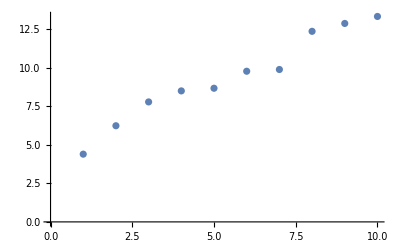

```mathematica
ListPlot[Log[Out[38]]]
```